```mathematica
(* Michael Barile 
68500 *)

(* 4.2 Problem #1 *)
(* Calculating lambda based off of given values of alpha, deltax and deltat *)
alpha=1/2;
deltax=.1;
deltat=.01;
lambda=alpha*deltat/deltax^2;
```

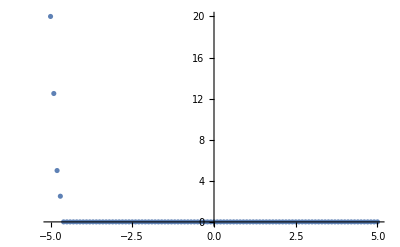

```mathematica
(* vector of x values from -5 to 5 in steps of deltax = 0.1 *)
xvec={-5};
x0=-5;
While[Max[xvec]<5,
x=x0+deltax;
AppendTo[xvec,x];
x0=x;
];
For[i=1,i≤Length[xvec],++i,
If[Abs[xvec[[i]]]<10^-5,
xvec[[i]]=0
];
];

(* temperature values along rod at time t = 0 *)
uvec={};
For[i=1,i≤Length[xvec],++i,
If[i==1,
AppendTo[uvec,20],
AppendTo[uvec,0]
];
];

(* Constructing matrix A *)

A={};
For[i=1,i≤Length[xvec],++i,
inew={};
For[j=1,j≤Length[xvec],++j,
If[j==i,
AppendTo[inew,1-2*lambda],
If[j==i-1||j==i+1,
AppendTo[inew,lambda],
AppendTo[inew,0]
];
];
];
AppendTo[A,inew]
];

(* Constructing and replacing top and bottom rows in matrix A to fix the first and last entry of uvec *)

toprow={};
For[i=1,i≤Length[xvec],++i,
If[i==1,
AppendTo[toprow,1],
AppendTo[toprow,0]
];
];

bottomrow={};
For[i=1,i≤Length[xvec],++i,
If[i==Length[xvec],
AppendTo[bottomrow,1],
AppendTo[bottomrow,0]
];
];
A[[1]]=toprow;
A[[Length[xvec]]]=bottomrow;


(* temperature plotted as a function of position at time t = .03, .06, .08 and .10 *)
uvec3=uvec;
For[i=1,i≤3,++i,
unew=A.uvec3;
uvec3=unew
];

iter3={};
For[i=1,i≤Length[xvec],++i,
AppendTo[iter3,{xvec[[i]],uvec3[[i]]}]
];

ListPlot[iter3]
```

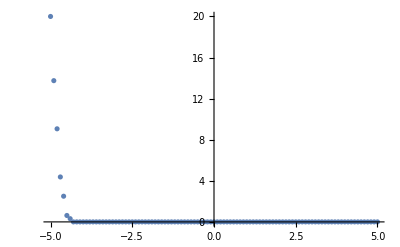

```mathematica
uvec6=uvec;
For[i=1,i≤6,++i,
unew=A.uvec6;
uvec6=unew
];

iter6={};
For[i=1,i≤Length[xvec],++i,
AppendTo[iter6,{xvec[[i]],uvec6[[i]]}]
];

ListPlot[iter6]
```

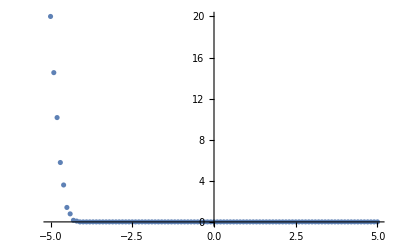

```mathematica
uvec8=uvec;
For[i=1,i≤8,++i,
unew=A.uvec8;
uvec8=unew
];

iter8={};
For[i=1,i≤Length[xvec],++i,
AppendTo[iter8,{xvec[[i]],uvec8[[i]]}]
];

ListPlot[iter8]
```

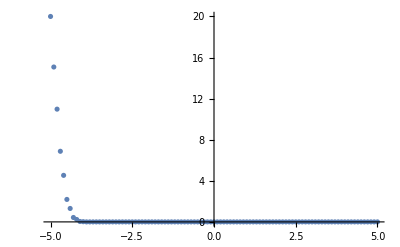

```mathematica
uvec10=uvec;
For[i=1,i≤10,++i,
unew=A.uvec10;
uvec10=unew
];

iter10={};
For[i=1,i≤Length[xvec],++i,
AppendTo[iter10,{xvec[[i]],uvec10[[i]]}]
];

ListPlot[iter10]
```

```mathematica
(* Constructing new matrix Amid where u at x=a and u at x=b are fixed, along with fixing u at x = 0 *)

Amid={};
For[i=1,i≤Length[xvec],++i,
inew={};
For[j=1,j≤Length[xvec],++j,
If[j==i,
AppendTo[inew,1-2*lambda],
If[j==i-1||j==i+1,
AppendTo[inew,lambda],
AppendTo[inew,0]
];
];
];
AppendTo[Amid,inew]
];

toprowmid={};
For[i=1,i≤Length[xvec],++i,
If[i==1,
AppendTo[toprowmid,1],
AppendTo[toprowmid,0]
];
];

bottomrowmid={};
For[i=1,i≤Length[xvec],++i,
If[i==Length[xvec],
AppendTo[bottomrowmid,1],
AppendTo[bottomrowmid,0]
];
];

midrow={};
For[i=1,i≤Length[xvec],++i,
If[i==51,
AppendTo[midrow,1],
AppendTo[midrow,0]
];
];

Amid[[1]]=toprowmid;
Amid[[Length[xvec]]]=bottomrowmid;
Amid[[51]]=midrow;

(* Constructing new initial vector for u at time 0, where the temperature at x=0 is 20 and everywhere else it is zero.  Furthermore, temp remains fixed at 20 at x=0, and fixed at x=-5, x=5 at 0 *)

uvecmid={};
For[i=1,i≤Length[xvec],++i,
If[i==51,
AppendTo[uvecmid,20],
AppendTo[uvecmid,0]
];
];
```

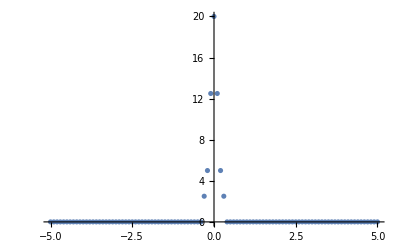

```mathematica
(* Plotting temperature as a function of position at t=0.3, 0.6, 0.8 and 0.10 *)

uvecmid3=uvecmid;
For[i=1,i≤3,++i,
unew=Amid.uvecmid3;
uvecmid3=unew
];

itermid3={};
For[i=1,i≤Length[xvec],++i,
AppendTo[itermid3,{xvec[[i]],uvecmid3[[i]]}]
];

ListPlot[itermid3]
```

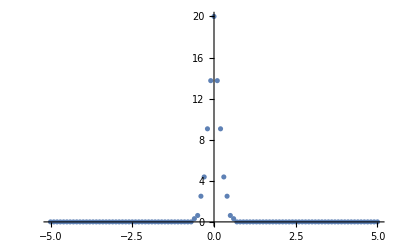

```mathematica
uvecmid6=uvecmid;
For[i=1,i≤6,++i,
unew=Amid.uvecmid6;
uvecmid6=unew
];

itermid6={};
For[i=1,i≤Length[xvec],++i,
AppendTo[itermid6,{xvec[[i]],uvecmid6[[i]]}]
];

ListPlot[itermid6]
```

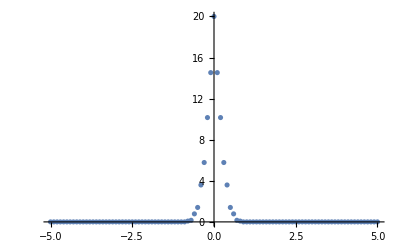

```mathematica
uvecmid8=uvecmid;
For[i=1,i≤8,++i,
unew=Amid.uvecmid8;
uvecmid8=unew
];

itermid8={};
For[i=1,i≤Length[xvec],++i,
AppendTo[itermid8,{xvec[[i]],uvecmid8[[i]]}]
];

ListPlot[itermid8]
```

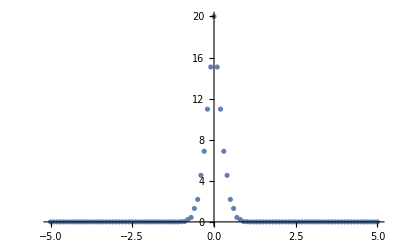

```mathematica
uvecmid10=uvecmid;
For[i=1,i≤10,++i,
unew=Amid.uvecmid10;
uvecmid10=unew
];

itermid10={};
For[i=1,i≤Length[xvec],++i,
AppendTo[itermid10,{xvec[[i]],uvecmid10[[i]]}]
];

ListPlot[itermid10,PlotRange->All]
```

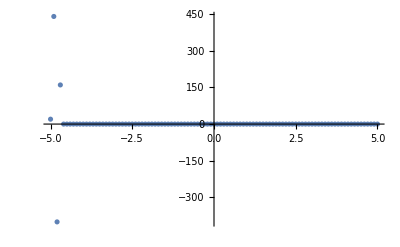

```mathematica
(* Problem # 2 *)
(* Calculating lambda with same deltax and deltat above, but with alpha = 2 *)

alpha=2;
deltax=.1;
deltat=.01;
lambda=alpha*deltat/deltax^2;

(* vector of x values from -5 to 5 in steps of deltax = 0.1 *)
xvec={-5};
x0=-5;
While[Max[xvec]<5,
x=x0+deltax;
AppendTo[xvec,x];
x0=x;
];
For[i=1,i≤Length[xvec],++i,
If[Abs[xvec[[i]]]<10^-5,
xvec[[i]]=0
];
];

(* temperature values along rod at time t = 0 *)
uvec={};
For[i=1,i≤Length[xvec],++i,
If[i==1,
AppendTo[uvec,20],
AppendTo[uvec,0]
];
];

(* Constructing matrix A *)

A={};
For[i=1,i≤Length[xvec],++i,
inew={};
For[j=1,j≤Length[xvec],++j,
If[j==i,
AppendTo[inew,1-2*lambda],
If[j==i-1||j==i+1,
AppendTo[inew,lambda],
AppendTo[inew,0]
];
];
];
AppendTo[A,inew]
];

(* Constructing and replacing top and bottom rows in matrix A to fix the first and last entry of uvec *)

toprow={};
For[i=1,i≤Length[xvec],++i,
If[i==1,
AppendTo[toprow,1],
AppendTo[toprow,0]
];
];

bottomrow={};
For[i=1,i≤Length[xvec],++i,
If[i==Length[xvec],
AppendTo[bottomrow,1],
AppendTo[bottomrow,0]
];
];
A[[1]]=toprow;
A[[Length[xvec]]]=bottomrow;


(* temperature plotted as a function of position at time t = .03, .06, .08 and .10 *)
(* We can see from the plots below that the results are not well-behaved *)

uvec3=uvec;
For[i=1,i≤3,++i,
unew=A.uvec3;
uvec3=unew
];

iter3={};
For[i=1,i≤Length[xvec],++i,
AppendTo[iter3,{xvec[[i]],uvec3[[i]]}]
];

ListPlot[iter3]
```

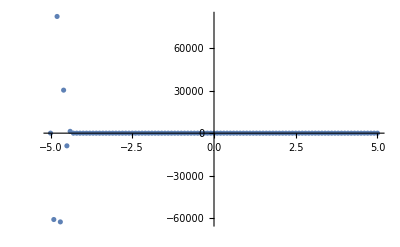

```mathematica
uvec6=uvec;
For[i=1,i≤6,++i,
unew=A.uvec6;
uvec6=unew
];

iter6={};
For[i=1,i≤Length[xvec],++i,
AppendTo[iter6,{xvec[[i]],uvec6[[i]]}]
];

ListPlot[iter6]
```

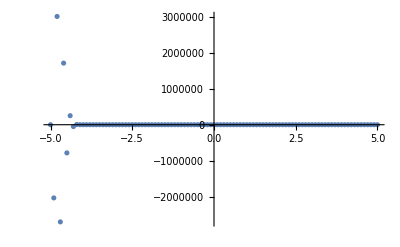

```mathematica
uvec8=uvec;
For[i=1,i≤8,++i,
unew=A.uvec8;
uvec8=unew
];

iter8={};
For[i=1,i≤Length[xvec],++i,
AppendTo[iter8,{xvec[[i]],uvec8[[i]]}]
];

ListPlot[iter8]
```

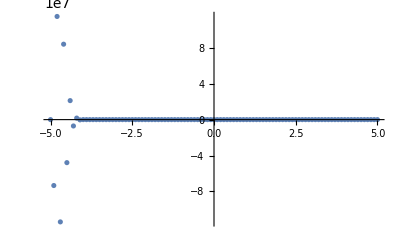

```mathematica
uvec10=uvec;
For[i=1,i≤10,++i,
unew=A.uvec10;
uvec10=unew
];

iter10={};
For[i=1,i≤Length[xvec],++i,
AppendTo[iter10,{xvec[[i]],uvec10[[i]]}]
];

ListPlot[iter10]
```

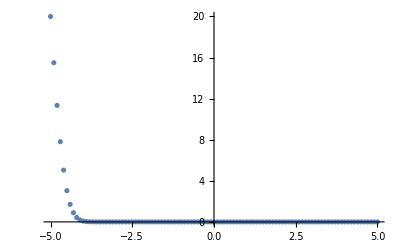

```mathematica
(* Problem #3 *)

alpha=2;
deltax=.1;
deltat=.001;
lambda=alpha*deltat/(deltax)^2;

(* vector of x values from -5 to 5 in steps of deltax = 0.1 *)
xvec={-5};
x0=-5;
While[Max[xvec]<5,
x=x0+deltax;
AppendTo[xvec,x];
x0=x;
];
For[i=1,i≤Length[xvec],++i,
If[Abs[xvec[[i]]]<10^-5,
xvec[[i]]=0
];
];

(* temperature values along rod at time t = 0 *)
uvec={};
For[i=1,i≤Length[xvec],++i,
If[i==1,
AppendTo[uvec,20],
AppendTo[uvec,0]
];
];

(* Constructing matrix A *)

A={};
For[i=1,i≤Length[xvec],++i,
inew={};
For[j=1,j≤Length[xvec],++j,
If[j==i,
AppendTo[inew,1-2*lambda],
If[j==i-1||j==i+1,
AppendTo[inew,lambda],
AppendTo[inew,0]
];
];
];
AppendTo[A,inew]
];

(* Constructing and replacing top and bottom rows in matrix A to fix the first and last entry of uvec *)

toprow={};
For[i=1,i≤Length[xvec],++i,
If[i==1,
AppendTo[toprow,1],
AppendTo[toprow,0]
];
];

bottomrow={};
For[i=1,i≤Length[xvec],++i,
If[i==Length[xvec],
AppendTo[bottomrow,1],
AppendTo[bottomrow,0]
];
];
A[[1]]=toprow;
A[[Length[xvec]]]=bottomrow;


(* temperature plotted as a function of position at time t = .03, .06, .08 and .10, but with time steps of deltat=.001.  We expect results to be well-behaved since lamba ≤ .5 *)
uvec3=uvec;
For[i=1,i≤30,++i,
unew=A.uvec3;
uvec3=unew
];

iter3={};
For[i=1,i≤Length[xvec],++i,
AppendTo[iter3,{xvec[[i]],uvec3[[i]]}]
];

ListPlot[iter3,PlotRange->All]
```

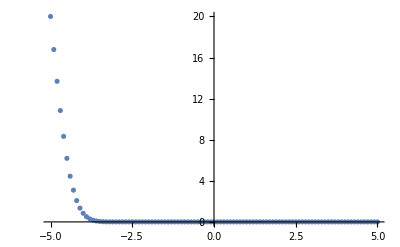

```mathematica
uvec6=uvec;
For[i=1,i≤60,++i,
unew=A.uvec6;
uvec6=unew
];

iter6={};
For[i=1,i≤Length[xvec],++i,
AppendTo[iter6,{xvec[[i]],uvec6[[i]]}]
];

ListPlot[iter6,PlotRange->All]
```

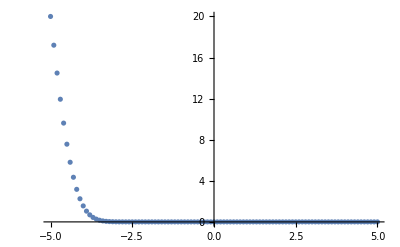

```mathematica
uvec8=uvec;
For[i=1,i≤80,++i,
unew=A.uvec8;
uvec8=unew
];

iter8={};
For[i=1,i≤Length[xvec],++i,
AppendTo[iter8,{xvec[[i]],uvec8[[i]]}]
];

ListPlot[iter8,PlotRange->All]
```

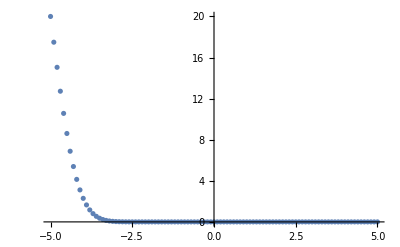

```mathematica
uvec10=uvec;
For[i=1,i≤100,++i,
unew=A.uvec10;
uvec10=unew
];

iter10={};
For[i=1,i≤Length[xvec],++i,
AppendTo[iter10,{xvec[[i]],uvec10[[i]]}]
];

ListPlot[iter10,PlotRange->All]
```